```mathematica
(* Задача 1 *)
P[x_,y_]:=x y^2
Q[x_,y_]:=2 x^2 y
(*Integrate[∇_{x,y} ×{P[x,y],Q[x,y]},{x,y}∈Disk[{0,0},2]]
Integrate[Curl[{x y^2,2 x^2 y},{x,y}],{x,y}∈Disk[{0,0},2]]*)
Integrate[D[Q[x,y], x]-D[P[x,y], y],{x,y}∈Triangle[{{0,0},{2,2},{2,4}}]]
Integrate[4x y-2 x y,{x,y}∈Triangle[{{0,0},{2,2},{2,4}}]]

P[x_,y_]:=y^3
Q[x_,y_]:=-x^3
Integrate[D[Q[x,y], x]-D[P[x,y], y],{x,y}∈Disk[{0,0},2]]
```

12

12

-24 π

```mathematica
(* Задача 2 *)
F[x_,y_]:={x(x+y), x y^2}
Integrate[D[(F[x,y]⟦2⟧), x]-D[(F[x,y]⟦1⟧), y],{x,y}∈Triangle[{{0,0},{1,0},{1,1}}]]
Integrate[∇_{x,y} ×F[x,y],{x,y}∈Triangle[{{0,0},{1,0},{1,1}}]]
```

-1/4

-1/4

```mathematica
(* Задача 3 *)
F[x_,y_]:=1/2{-y, x}
r[θ_]:=2(1-Cos[θ])
Integrate[F[r[θ]Cos[θ],r[θ]Sin[θ]].{D[(r[θ]Cos[θ]), θ],D[(r[θ]Sin[θ]), θ]},{θ, 0, 2Pi}]
```

6 π

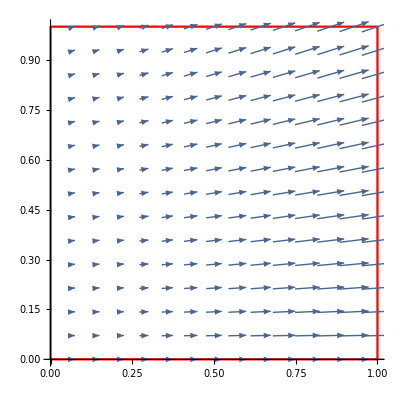

True

```mathematica
(* Задача 4 *)
F[x_,y_]:={3x, x y}
interNalIntegral =Integrate[∇_{x,y} .F[x,y],{x,0,1},{y,0,1}];
Show[{
ListLinePlot[{{0,0},{1,0},{1,1},{0,1},{0,0}},PlotRange->All,AspectRatio->1,PlotStyle->Red],
VectorPlot[F[x,y],{x,0,1},{y,0,1}]}]
curveIntegral = Integrate[F[t,0].{0,-1},{t,0,1}] + Integrate[F[1,t].{1,0},{t,0,1}]+ Integrate[F[1-t,1].{0,1},{t,0,1}]+Integrate[F[0,1-t].{-1,0},{t,0,1}];
interNalIntegral == curveIntegral
```

```mathematica
(* Задача 5 *)
F[x_,y_,z_]:={x y Exp[z], x y^2 z^3, -y Exp[z]}
Integrate[∇_{x,y,z} .F[x,y,z],{x,0,3},{y,0,2},{z,0,1}]
```

9/2